# Photos for the paper

Author: Belgin Seymenoglu; 
based on Steve Baigent’s original code

This notebook produces phase plots for the Nagylaki-Crow model proposed in 1974. I used it to make the figures for my paper and conference talks about the model.

## 1. Plotting phase planes and manifolds

Sets up the Nagylaki-Crow model. You can put different values for the fertility and mortality parameters by changing the numbers in r3 or by pasting examples from Appendix A; this should change the phase plot

g1=

1.08825-3.653 x^3+x^2 (7.69425-23.506 y)-2.1765 y+1.08825 y^2+x (-5.1295+6.1825 y-2.653 y^2)

g2=

1.08825+x^2 (1.08825-3.653 y)-4.4295 y+5.99425 y^2-2.653 y^3+x (-2.1765+6.8825 y-23.506 y^2)

At x=0, g1=

1.08825 (1.-1. y)^2

At y=0, g2=

1.08825 (1.-1. x)^2

******************************

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0,y→1.},{x→0.000573686,y→0.970626},{x→0.175453,y→0.243682},{x→0.179431-0.401649 ⅈ,y→0.0961094-0.38228 ⅈ},{x→0.179431+0.401649 ⅈ,y→0.0961094+0.38228 ⅈ},{x→0.963893,y→0.00117345},{x→1.,y→0}}

Total number of fixed points:7

Number of fixed points inside the simplex:5

{{0,1.},{0.000573686,0.970626},{0.175453,0.243682},{0.963893,0.00117345},{1.,0}}

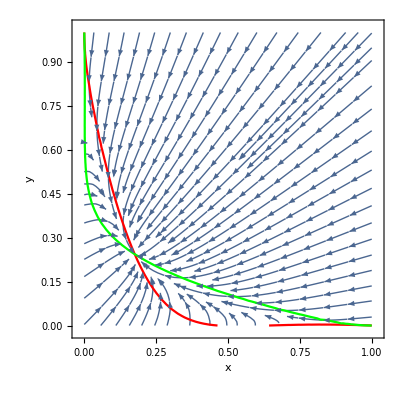

at (0,1)

(-1.6 | 0.
-18.8 | -0.4)

{{-1.6,-0.4},{{0.0637002,0.997969},{0.,1.}}}

{{0.0637002,0.997969},{0.,1.}}

15.6667

at (1,0)

(-0.7 | -19.5
0. | -1.2)

{{-1.2,-0.7},{{0.999671,0.0256326},{1.,0.}}}

{{0.999671,0.0256326},{1.,0.}}

0.025641

```mathematica
n=2;
(*Next two replacement rules enforce symmetry rules on the fertilities*)
r={Subscript[a, 1,2,1,1]->Subscript[a, 1,1,1,2],Subscript[a, 1,1,2,1]-> Subscript[a, 2,1,1,1],Subscript[a, 2,2,1,2]->Subscript[a, 1,2,2,2],Subscript[a, 2,1,2,2]->Subscript[a, 2,2,2,1],Subscript[a, 1,1,2,2]->Subscript[a, 2,2,1,1],Subscript[a, 1,2,2,1]->Subscript[a, 2,1,1,2],Subscript[d, 2,1]->Subscript[d, 1,2]};
rs={ Subscript[a, 2,1,1,1]->Subscript[a, 1,1,1,2],Subscript[a, 2,2,2,1]-> Subscript[a, 1,2,2,2],Subscript[a, 2,1,2,1]-> Subscript[a, 1,2,1,2],Subscript[a, 2,1,1,2]->Subscript[a, 1,2,1,2] };
(*Constants are relabelled as follows:*)
r2={Subscript[d, 1,1]->D1,Subscript[d, 2,2]->D3,Subscript[d, 1,2]->D2,Subscript[a, 1,1,1,1]->F11,Subscript[a, 1,1,1,2]->F12,Subscript[a, 1,2,1,2]->F22,Subscript[a, 2,2,1,1]->F13,Subscript[a, 1,2,2,2]->F23,Subscript[a, 2,2,2,2]->F33};
r3={D1->0.3,D3->0.2,D2->0.7,F11->1.3,F12->1.0,F22->4.353,F13->10,F23->1.6,F33->1.5};

S=Table[(∑_(k=1)^n ∑_(l=1)^n Subscript[a, i,k,l,j] Subscript[P, i,k] Subscript[P, l,j]-Subscript[d, i,j] Subscript[P, i,j])-Subscript[P, i,j]∑_(u=1)^n ∑_(v=1)^n (∑_(k=1)^n ∑_(l=1)^n Subscript[a, u,k,l,v] Subscript[P, u,k] Subscript[P, l,v]-Subscript[d, u,v] Subscript[P, u,v]),{i,n},{j,n}]/.r/.rs/.r2/.r3;
T=S/.{Subscript[P, 1,1]->x,Subscript[P, 1,2]->z/2,Subscript[P, 2,1]->z/2,Subscript[P, 2,2]->y};
T1=T/.{z->1-x-y};

f1=FullSimplify[T1[[1,1]]];
f2=FullSimplify[T1[[2,2]]];

Print["g1="]
g1=Collect[f1,{x,y}]
Print["g2="]
g2=Collect[f2,{x,y}]
Print["At x=0, g1="]
FullSimplify[g1/.x->0]
Print["At y=0, g2="]
FullSimplify[g2/.y->0]
Print["******************************"]

steadies=Chop[Solve[{g1==0.,g2==0.},{x,y}] ]
fixeds={x,y}/.steadies;
Print["Total number of fixed points:", Length[fixeds]]
check[x_,y_]:=NonNegative[x]&&NonNegative[y]&&NonNegative[1-x-y]
dottyuns=Reap[Do[Sow[fixeds[[j]],check[#[[1]],#[[2]]]&[fixeds[[j]]]],{j,Length[fixeds]}],True][[2,1]];
dotty=Sort[dottyuns,#1[[1]]<#2[[1]]&];
Print["Number of fixed points inside the simplex:", Length[dotty]]
Print[dotty]

s=1;
k=0.;

p1=ContourPlot[g1==0,{x,k,s},{y,k,s},ContourStyle->Red];
p2=ContourPlot[g2==0,{x,k,s},{y,k,s},ContourStyle->Green];
p3=Show[{p1,p2}];

h1=StreamPlot[{g1,g2},{x,k,s},{y,k,s}];
h2=RegionPlot[x+y≥1,{x,k,s},{y,k,s},PlotStyle->White];
spot=Graphics[{PointSize[0.015],Point[dotty]}];
Show[h1,p3,Frame->True,FrameLabel->{x,y},LabelStyle->Directive[Medium]]
(*Show[{h3,p3}]
Show[{h4,p3}]*)

J=({{D[g1,x], D[g1,y]}, {D[g2,x], D[g2,y]}});
Print["at (0,1)"]
M2=Simplify[J/.{x->0,y->1}];
MatrixForm[M2]
Eigensystem[M2]
v=Eigensystem[M2][[2]]
v[[1,2]]/v[[1,1]]
Print["at (1,0)"]

M=Simplify[J/.{x->1,y->0}];
MatrixForm[M]
Eigensystem[M]
v=Eigensystem[M][[2]]
v[[1,2]]/v[[1,1]]
```

The next two cells should allow you to plot manifolds, as well as nullclines.

```mathematica
fn1=g1/.{x->x[t],y->y[t]};
fn2=g2/.{x->x[t],y->y[t]};
tmax=150;error=10^-4;

orbitleft=Table[NDSolve[{x'[t]==fn1,y'[t]==fn2,x[0]==dotty[[j,1]]-error,y[0]==dotty[[j,2]]+error},{x,y},{t,0,tmax}],{j,Length[dotty]}];
orbitright=Table[NDSolve[{x'[t]==fn1,y'[t]==fn2,x[0]==dotty[[j,1]]+error,y[0]==dotty[[j,2]]-error},{x,y},{t,0,tmax}],{j,Length[dotty]}];

plotleft=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.orbitleft[[j]]],{t,0,tmax},PlotStyle->{Magenta,Thick}],{j,Length[dotty]}];
plotright=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.orbitright[[j]]],{t,0,tmax},PlotStyle->{Magenta,Thick}],{j,Length[dotty]}];
```

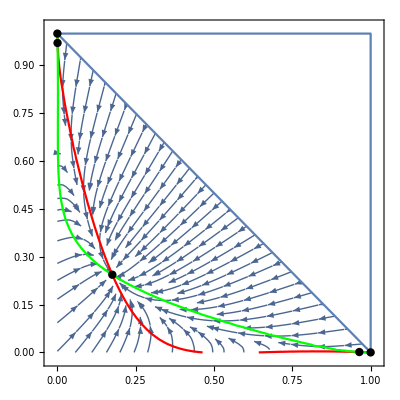

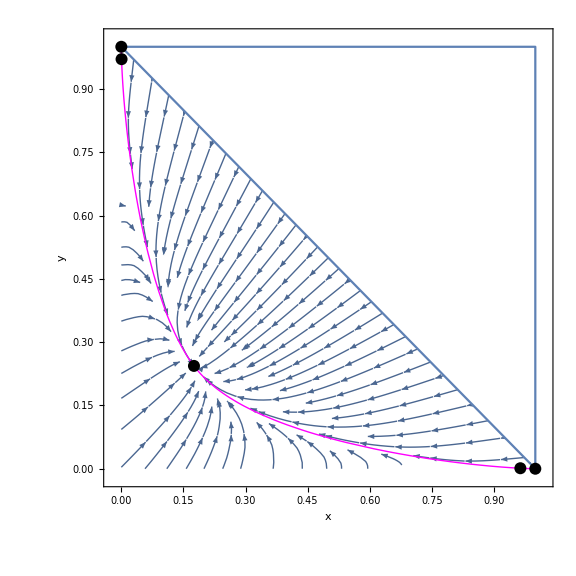

```mathematica
Show[h1,h2,p3,spot]
manif={h1,h2};
n=Length[dotty]-1;Do[AppendTo[manif,plotleft[[j+1]]],{j,1,n}]
Do[AppendTo[manif,plotright[[j]]],{j,1,n}]
AppendTo[manif,spot];
Show[manif,ImageSize->Large,Frame->True,FrameLabel->{x,y},LabelStyle->Directive[Medium]]
```

Only run this cell if your parameters give a Hardy-Weinberg manifold for the model. This is known to happen when the fertilities and death rates are additive.

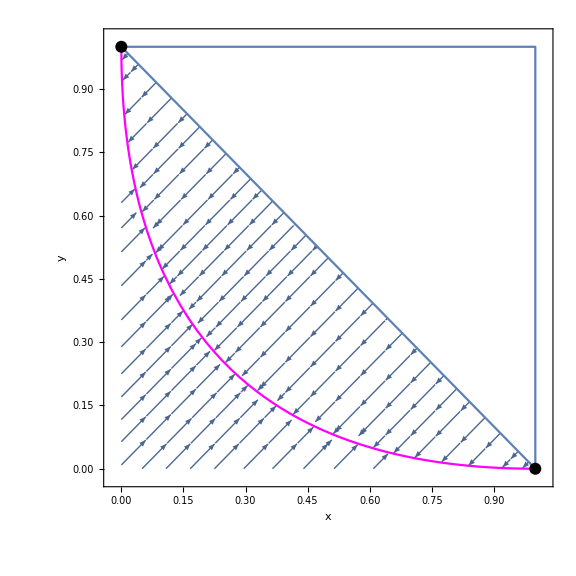

```mathematica
spot=Graphics[{PointSize[0.015],Point[{{0,1},{1,0}}]}];
hw=Plot[1+x-2 Sqrt[x],{x,0,1},PlotStyle->Magenta];
Show[h1,h2,hw,spot,ImageSize->Large,Frame->True,FrameLabel->{x,y},LabelStyle->Directive[Medium]]
```

Only run this cell for the non-convex example. It shows a blow-up of the phase plot near the fixed point (0,1).

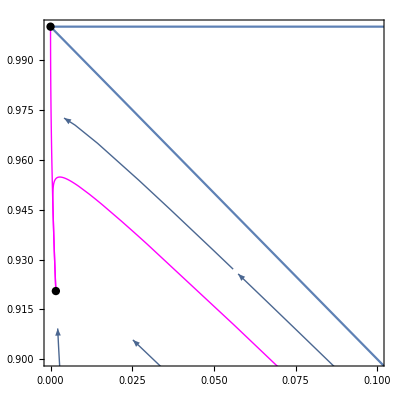

```mathematica
Show[Show[Delete[ manif,3]],PlotRange->{{0,0.1},{.9,1}}]
```

## 2. The argument for the existence of the manifold

Replace r3 in Section 1 with these parameter values, then run the entire section.

```mathematica
r3={D1->0.3,D3->0.2,D2->0.7,F11->1.3,F12->1.0,F22->4.353,F13->10,F23->1.6,F33->1.5};
```

Now run the next cell to make Figure (3 a) from the paper :

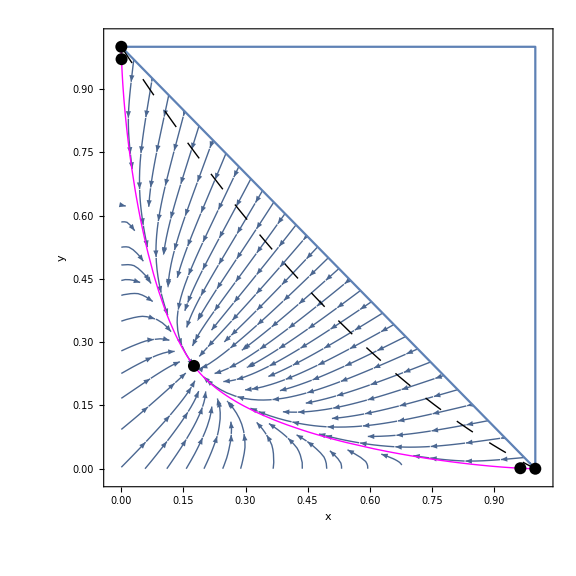

```mathematica
ϵ=0.5;
starting=Plot[{(1-x)(1-ϵ x)},{x,0,1},PlotStyle->{Thick,Black,Dashing[Large]}];
Show[manif,starting,ImageSize->Large,Frame->True,FrameLabel->{x,y},LabelStyle->Directive[Medium]]
```

Run the rest of this section to produce and export Figure (3b) from the paper. It basically gives you the phase plot for the (w,t) coordinates proposed by Koth and Kemler.

******************************

FIXED POINTS

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{w→-0.324515-0.75767 ⅈ,t→-0.403819-0.618384 ⅈ},{w→-0.324515+0.75767 ⅈ,t→-0.403819+0.618384 ⅈ},{w→0.0398393,t→67.4045},{w→0.60411,t→0.839032},{w→55.1851,t→0.0671827}}

Total number of fixed points: 5

Number of fixed points inside the quadrant: 3

{{0.0398393,67.4045},{0.60411,0.839032},{55.1851,0.0671827}}

******************************

EIGENVALUES

At (0,1), eigenvalues are λ1=-1.6 and λ2=-0.4.

λ2-λ1=1.2

While at (1,0), eigenvalues are λ1=-1.2 and λ2=-0.7.

λ2-λ1=0.5

Competitive

******************************

VERTICAL NULLCLINE

Horizontal asymptote: 0.07

Vertical asymptotes: 0 and -0.12

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Stationary points:{w→-0.0593379,w→5.3776}

******************************

HORIZONTAL NULLCLINE

Horizontal asymptotes: 0 and -0.05

Vertical asymptote: 0.04

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

'Stationary' points:{t→-0.0249876,t→50.3487}

******************************

PHASE PLOT

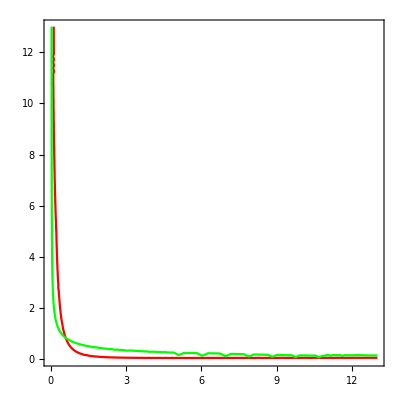

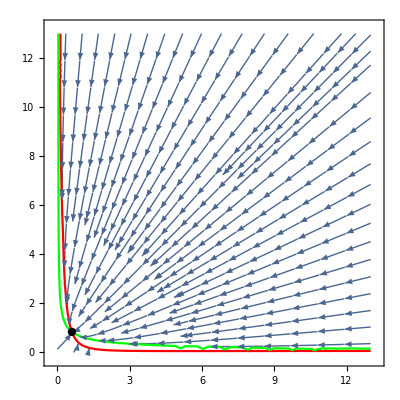

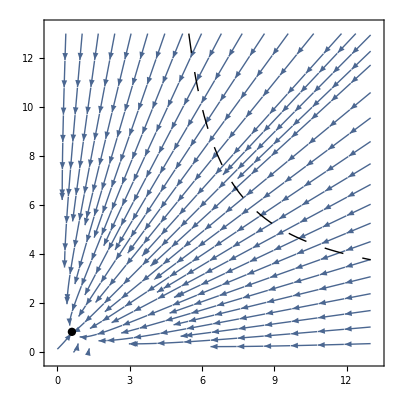

```mathematica
r2={D1->0.3,D3->0.2,D2->0.7,F11->1.3,F12->1.0,F22->4.353,F13->10,F23->1.6,F33->1.5};
q1=(F11-F12+D2-D1)w^2+(2(F12+D2-D1)-F22)w+F22-w t(F23-D2+D1+F13 w);
q2=(F33-F23+D2-D3)t^2+(2(F23+D2-D3)-F22)t+F22-w t(F12-D2+D3+F13 t);
Print["******************************"]
Print["FIXED POINTS"]
steadies=Chop[Solve[{(q1/.r2)==0.,(q2/.r2)==0.},{w,t}] ]
fixeds={w,t}/.steadies;
Print["Total number of fixed points: ", Length[fixeds]]
check[w_,t_]:=NonNegative[w]&&NonNegative[t]
choosy=Reap[Do[Sow[fixeds[[j]],check[#[[1]],#[[2]]]&[fixeds[[j]]]],{j,Length[fixeds]}],True];
If[choosy[[2]]=={},dottyuns={},dottyuns=choosy[[2,1]]];
dotty=Sort[dottyuns,#1[[1]]<#2[[1]]&];
Print["Number of fixed points inside the quadrant: ", Length[dotty]]
Print[dotty]
Print["******************************"]
Print["EIGENVALUES"]
λ01one=(D3-D1-F33)/.r2;
λ01two=(D3-D2+F23-F33)/.r2;
λ10one=(D1-D3-F11)/.r2;
λ10two=(D1-D2+F12-F11)/.r2;
diff01=λ01two-λ01one;
diff10=λ10two-λ10one;
Print["At (0,1), eigenvalues are ","λ1","=",λ01one," and ","λ2","=",λ01two,"."]
Print["λ2-λ1","=",diff01]
Print["While at (1,0), eigenvalues are ","λ1","=",λ10one," and ","λ2","=",λ10two,"."]
Print["λ2-λ1","=",diff10]
check[w_,t_]:=NonNegative[w]&&NonNegative[t]
If[check[diff01,diff10],Print["Competitive"],Print["Not competitive"]]
Print["******************************"]
Print["VERTICAL NULLCLINE"]
Print["Horizontal asymptote: ",-λ10two/(F13/.r2)]
Print["Vertical asymptotes: ",0," and ",-diff01/(F13/.r2)]

min=Flatten[Solve[(D[(F22-2 D1 w+2 D2 w+2 F12 w-F22 w-D1 w^2+D2 w^2+F11 w^2-F12 w^2)/(w (D1-D2+F23+F13 w)),w]/.r2)==0,w,Reals]];Print["Stationary points:",min]
Print["******************************"]
Print["HORIZONTAL NULLCLINE"]
Print["Horizontal asymptotes: ",0," and ",-diff10/(F13/.r2)]
Print["Vertical asymptote: ",-λ01two/(F13/.r2)]
minvert=Flatten[Solve[(D[(F22+2 D2 t-2 D3 t-F22 t+2 F23 t+D2 t^2-D3 t^2-F23 t^2+F33 t^2)/(t (-D2+D3+F12+F13 t)),t]/.r2)==0,t,Reals]];Print["'Stationary' points:",minvert]
Print["******************************"]
Print["PHASE PLOT"]

s=13;
k=0;

p1=ContourPlot[(q1/.r2)==0,{w,k,s},{t,k,s},ContourStyle->Red];
p2=ContourPlot[(q2/.r2)==0,{w,k,s},{t,k,s},ContourStyle->Green];
p3=Show[{p1,p2}]


h1=StreamPlot[{q1/.r2,q2/.r2},{w,k,s},{t,k,s}];
spot=Graphics[{PointSize[0.015],Point[dotty]}];
Show[{h1,p3,spot}]

ϵ=0.5;startingw=Plot[{(-2(2+w-w ϵ))/(2-w ϵ)},{w,4.1,s},PlotStyle->{Thick,Black,Dashing[Large]},PlotRange->{{0,s},{0,s}}];
Show[{h1,spot,startingw}]
```

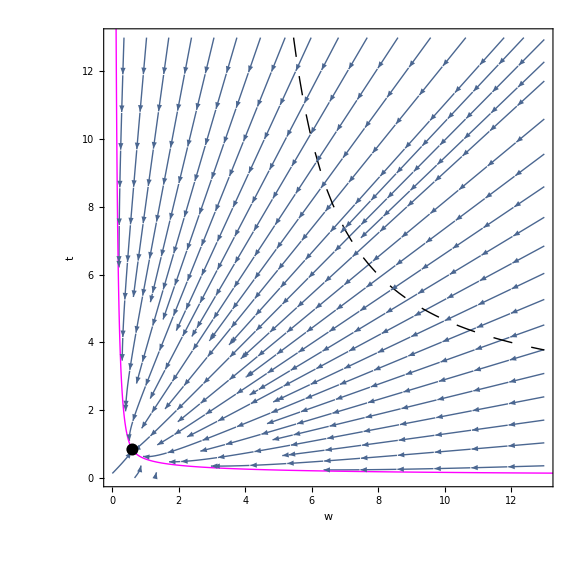

```mathematica
tmax=20;error=10^-4;
plotleftwt=Table[ParametricPlot[Evaluate[{(2 x[t])/(1-x[t]-y[t]),(2 y[t])/(1-x[t]-y[t])}/.orbitleft[[j]]],{t,0,tmax},PlotStyle->{Thick,Magenta}],{j,2,4}];
plotrightwt=Table[ParametricPlot[Evaluate[{(2 x[t])/(1-x[t]-y[t]),(2 y[t])/(1-x[t]-y[t])}/.orbitright[[j]]],{t,0,tmax},PlotStyle->{Thick,Magenta}],{j,2,4}];

manif={h1,startingw};
Do[AppendTo[manif,plotleftwt[[j+1]]],{j,0,2}]
Do[AppendTo[manif,plotrightwt[[j]]],{j,1,3}]
AppendTo[manif,spot];
Show[manif,PlotRange->{{0,s},{0,s}},ImageSize->Large,Frame->True,FrameLabel->{w,t},LabelStyle->Directive[Medium]]
```

For exporting photos at a higher resolution:

```mathematica
Export["initialwt.png",%,ImageResolution->300]
```

initialwt.png

## A. Repository of examples to put in the paper and talks

### A.1 Figures in the paper

Five interior fixed points...(Figure 1 in paper)

```mathematica
r3={D1->2.,D3->2.,D2->1.,F11->6,F12->.5,F22->1/14,F13->1,F23->.5,F33->6};
```

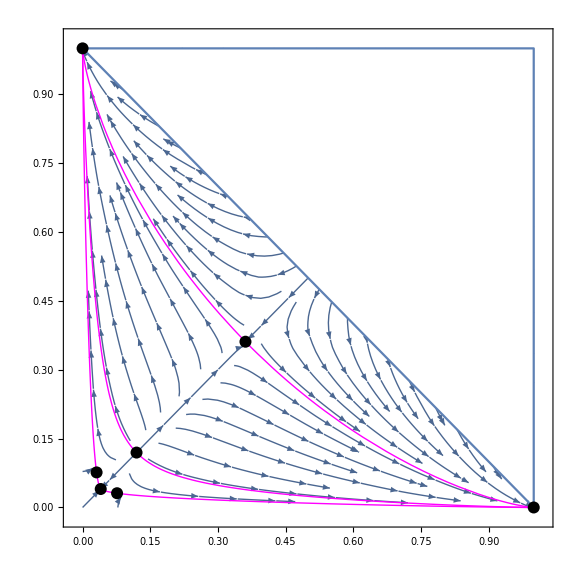

Hardy - Weinberg example (Figure 2 in paper)

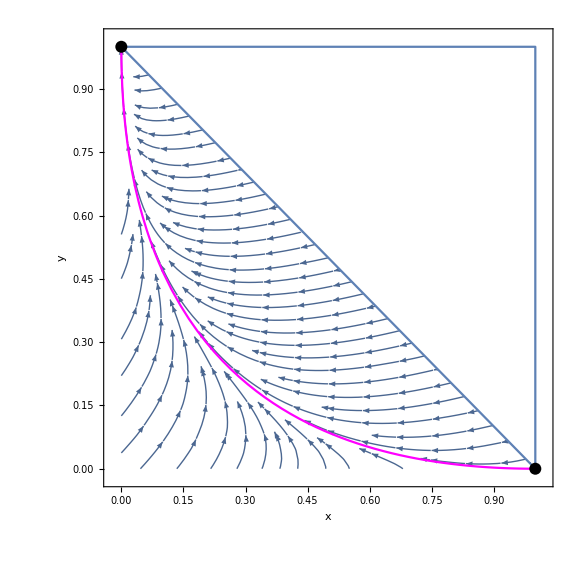

```mathematica
r3={D1->0.3,D3->0.2,D2->0.25,F11->.6,F12->.9,F22->1.2,F13->1.3,F23->1.6,F33->2};
```

Non - convex example:
a) With nullclines
b) Without nullclines (Figure 4 in paper)
c) Zoomed in near the fixed point (0,1)

It’s not globally competitive

```mathematica
r3={D1->93/100,D3->1/10,D2->9/10,F11->2/5,F12->1/100,F22->98/100,F13->1/81,F23->11/12,F33->1/97};
```

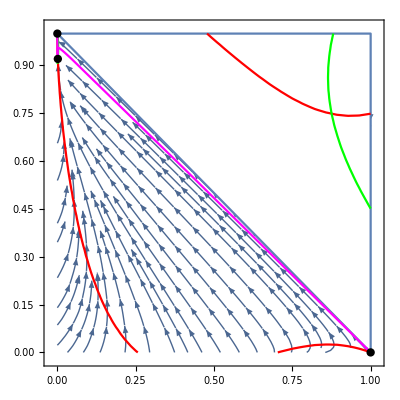

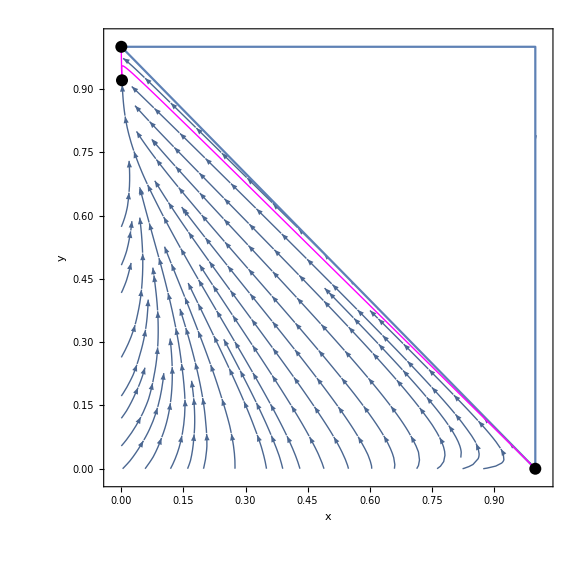

-Graphics-

### A.2 Examples not included in the paper (some were used in talks)

Pure fertility, with all fertilities equalling 1.

```mathematica
r3={D1->0,D3->0,D2->0,F11->1.,F12->1,F22->1,F13->1,F23->1,F33->1};
```

-Graphics-

Another example with three manifolds. Strictly speaking, these are called “heteroclinic chains” because each of them consist of multiple heteroclinic connections in the chain between the two fixation states (0,1) and (1,0). Moreover, the chains make up a decreasing function on the interval (0,1), hence no two points can be ordered using the standard partial order based on the first quadrant. Hence the chain is said to be “nonmonotone”.

 (competitive CHECK THIS!)

```mathematica
r3={D1->151/320,D3->3/32,D2->0,F11->249/160,F12->63/160,F22->3/64,F13->3/64,F23->1/64,F33->4/5};
```

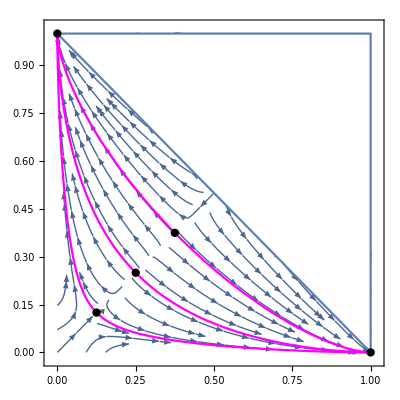

A pure fertility example with three interior fixed points...

```mathematica
r3={D1->0.,D3->0.,D2->0.,F11->4.55,F12->0.01,F22->4.353,F13->10,F23->.1,F33->2.89};
```

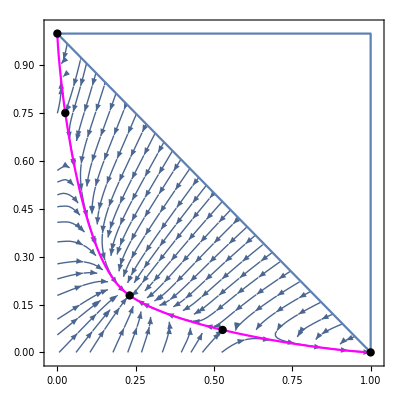

Example with no interior fixed points, i.e. only one “heteroclinic connection” in the chain between the two fixation states (0,1) and (1,0)

```mathematica
r3={D1->0,D3->0,D2->1/100,F11->2.5,F12->2.4,F22->1,F13->1,F23->2,F33->1};
```